# MAPK model (Kholodenko, BN, Sustained oscillations in MAPK cascades, European Journal of Biochemistry, 267, 1583-1588, 2000)

This is probably the first mathematica file that you see with a dynamic model of a molecular reaction network.  We will step by step explain the mathematica code for model specification and the computation of the dynamics.  We will make extensive of text and input cells, so you need to have looked at the Mathematica introduction file before you can work comfortably with this notebook.  (Throughout this notebook be aware of the different meanings of ‘=’,’==’, and ‘→’.)

## Kinetic model specification

### Mass balances

For every variable intermediate in the molecular reaction network we have a mass balance (an ordinary differential equation) that accounts for the rate of change in the concentration of a signaling intermediate given rates for production and consumption. dx/dtis denoted by x'[t] in Mathematica. Note that a differential equation requires ‘==’ and not ‘=’ but the naming of the list with all the differential equations in it again requires ‘=’!

```mathematica
massbalances = {
   raf'[t] == v2 - v1,
   rafp'[t] == v1 - v2,
   mek'[t] == v4 - v3,
   mekp'[t] == v3 - v4 - v5 + v6,
   mekpp'[t] == v5 - v6,
   erk'[t] == v8 - v7,
   erkp'[t] == v7 - v8 - v9 + v10,
   erkpp'[t] == v9 - v10};
```

### Rate equations

Rate equations express the rate of a reactions in terms of kinetic parameters and concentrations of reactants and effectors. Note that this is a substitution rule and requires usage of ‘⟶’ to make sure that v1 is not linked to its rate equation throughout the notebook.

```mathematica
rateequations={
v1->V1/(1+(erkpp[t]/Ki)^n) raf[t]/(K1+raf[t]),v2->V2 rafp[t]/(K2+rafp[t]),
v3->k3 rafp[t] mek[t]/(K3+mek[t]),v4->V4 mekp[t]/(K4+mekp[t]),v5->k5 rafp[t] mekp[t]/(K5+mekp[t]),v6->V6 mekpp[t]/(K6+mekpp[t]),v7->k7 mekpp[t] erk[t]/(K7+erk[t]),v8->V8 erkp[t]/(K8+erkp[t]),v9->k9 mekpp[t] erkp[t]/(K8+erkp[t]),v10->V10 erkpp[t]/(K10+erkpp[t])};
```

### Parameters

The kinetic parameters occuring in the rate equations need to be given a value. They are collected in a list using the substitution rule.

```mathematica
parameters={
V1->2.5,n->1,Ki->9,K1->10,V2->0.25,K2->8,
k3->0.025,K3->15,k5->0.025,K5->15,V4->0.75,K4->15,V6->0.75,K6->15,
k7->0.025,K7->15,k9->0.025,K9->15,V8->0.5,K8->15,V10->0.5,K10->15};
```

### Initial conditions

Initial conditions are differential equation properties and require usage of ‘==’.

```mathematica
initialconditions={
raf[0]==75,rafp[0]==25,
mek[0]==250,mekp[0]==25,mekpp[0]==25,
erk[0]==250,erkp[0]==25,erkpp[0]==25
};
```

### Integration of the differential equation

To integrate the mass balances over time we require the NDSolve routine.  First we substitute the rate equations and the kinetic parameters in the mass balances and the initial conditions to the list of mass balances. Then, we tell NDSolve what the variables are and for what period of time we would like to obtain the numerical solution to the differential equations.

```mathematica
Join[massbalances/.rateequations/.parameters,initialconditions]
```

{raf'[t]==-(2.5 raf[t])/((1+erkpp[t]/9) (10+raf[t]))+(0.25 rafp[t])/(8+rafp[t]),rafp'[t]==(2.5 raf[t])/((1+erkpp[t]/9) (10+raf[t]))-(0.25 rafp[t])/(8+rafp[t]),mek'[t]==(0.75 mekp[t])/(15+mekp[t])-(0.025 mek[t] rafp[t])/(15+mek[t]),mekp'[t]==-(0.75 mekp[t])/(15+mekp[t])+(0.75 mekpp[t])/(15+mekpp[t])+(0.025 mek[t] rafp[t])/(15+mek[t])-(0.025 mekp[t] rafp[t])/(15+mekp[t]),mekpp'[t]==-(0.75 mekpp[t])/(15+mekpp[t])+(0.025 mekp[t] rafp[t])/(15+mekp[t]),erk'[t]==(0.5 erkp[t])/(15+erkp[t])-(0.025 erk[t] mekpp[t])/(15+erk[t]),erkp'[t]==-(0.5 erkp[t])/(15+erkp[t])+(0.5 erkpp[t])/(15+erkpp[t])+(0.025 erk[t] mekpp[t])/(15+erk[t])-(0.025 erkp[t] mekpp[t])/(15+erkp[t]),erkpp'[t]==-(0.5 erkpp[t])/(15+erkpp[t])+(0.025 erkp[t] mekpp[t])/(15+erkp[t]),raf[0]==75,rafp[0]==25,mek[0]==250,mekp[0]==25,mekpp[0]==25,erk[0]==250,erkp[0]==25,erkpp[0]==25}

```mathematica
solution=NDSolve[Join[massbalances/.rateequations/.parameters,initialconditions],{raf,rafp,mek,mekp,mekpp,erk,erkp,erkpp},{t,0,10000}];
```

The solution to the system of differential equation is again a list with substitution rules.  If you want to know the concentration of raf at time 133.5 then you do substitute the solution at time point for raf.

```mathematica
raf[133.5]/.solution
```

{45.7163}

### Plotting of results

It is more informative to plot the solutions of a dynamic model simulation.  As you can see below, the model oscillates.  Try to change the parameters to make the oscillations slower, to speed them up, make them dampled, and remove them completely.

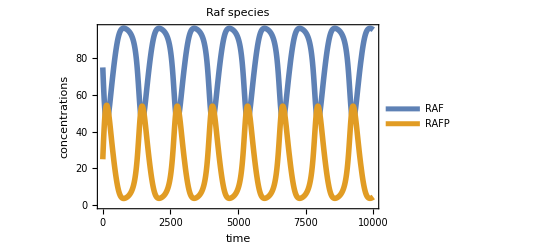

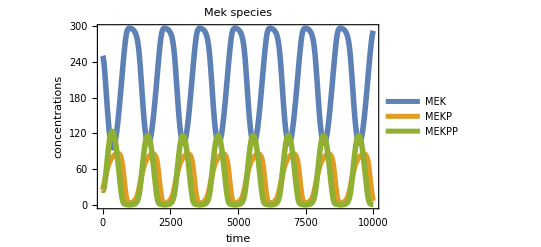

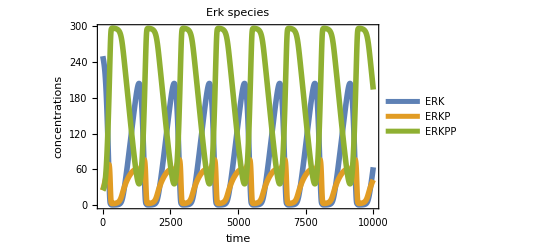

```mathematica
Plot[{raf[t]/.solution,rafp[t]/.solution},{t,0,10000},Frame->True,FrameLabel->{"time","concentrations"},BaseStyle->{FontFamily->"Gill Sans Light",FontSize->14},PlotStyle->Thickness[0.01],PlotLabel->"Raf species",PlotLegends->{"RAF","RAFP"}]

Plot[{mek[t]/.solution,mekp[t]/.solution,mekpp[t]/.solution},{t,0,10000},Frame->True,FrameLabel->{"time","concentrations"},BaseStyle->{FontFamily->"Gill Sans Light",FontSize->14},PlotStyle->Thickness[0.01],PlotLabel->"Mek species",PlotLegends->{"MEK","MEKP","MEKPP"}]

Plot[{erk[t]/.solution,erkp[t]/.solution,erkpp[t]/.solution},{t,0,10000},Frame->True,FrameLabel->{"time","concentrations"},BaseStyle->{FontFamily->"Gill Sans Light",FontSize->14},PlotStyle->Thickness[0.01],PlotLabel->"Erk species",PlotLegends->{"ERK","ERKP","ERKPP"}]
```

#### without feedback (n=0), no oscillations

```mathematica
solutionnof[nv_,V1v_]:=NDSolve[Join[massbalances/.rateequations/.n->nv/.V1->V1v/.parameters,initialconditions],{raf,rafp,mek,mekp,mekpp,erk,erkp,erkpp},{t,0,10000}];
```

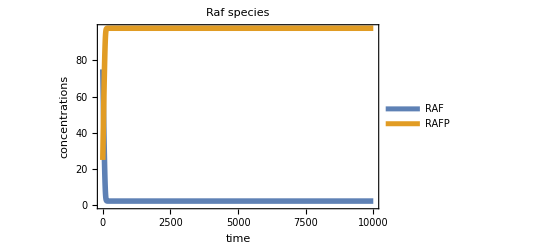

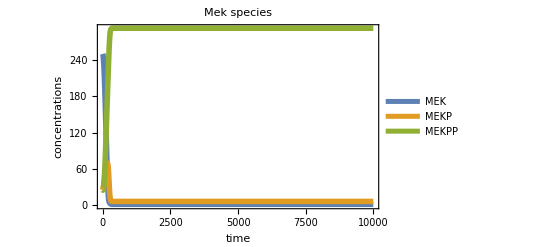

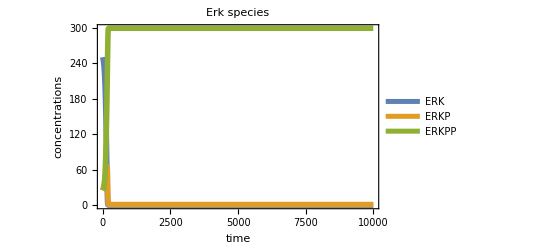

```mathematica
Plot[Evaluate[{raf[t],rafp[t]}/.solutionnof[0,2.5]],{t,0,10000},Frame->True,FrameLabel->{"time","concentrations"},BaseStyle->{FontFamily->"Gill Sans Light",FontSize->14},PlotStyle->Thickness[0.01],PlotLabel->"Raf species",PlotLegends->{"RAF","RAFP"}]

Plot[Evaluate[{mek[t],mekp[t],mekpp[t]}/.solutionnof[0,2.5]],{t,0,10000},Frame->True,FrameLabel->{"time","concentrations"},BaseStyle->{FontFamily->"Gill Sans Light",FontSize->14},PlotStyle->Thickness[0.01],PlotLabel->"Mek species",PlotLegends->{"MEK","MEKP","MEKPP"}]

Plot[Evaluate[{erk[t],erkp[t],erkpp[t]}/.solutionnof[0,2.5]],{t,0,10000},Frame->True,FrameLabel->{"time","concentrations"},BaseStyle->{FontFamily->"Gill Sans Light",FontSize->14},PlotStyle->Thickness[0.01],PlotLabel->"Erk species",PlotLegends->{"ERK","ERKP","ERKPP"}]
```

#### We can approximately calculate the value of the steady state of ERKPP by simulating for a long time and then pick its value (this does not work when it oscillates of course).

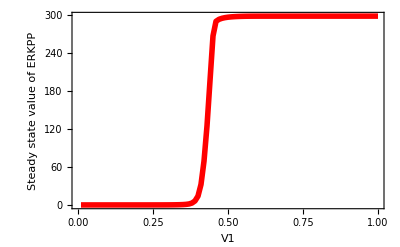

```mathematica
Table[{V1,erkpp[t]/.t->1000/.solutionnof[0,V1][[1]]},{V1,0.01,1,0.01}];
ListLinePlot[%,PlotRange->All,InterpolationOrder->1,Frame->True,FrameLabel->{"V1","Steady state value of ERKPP"},BaseStyle->FontSize->14,PlotStyle->{Thickness[0.01],Red}]
```